### Chapter X 2D and 3D Graphics

Free form plots:
1. Ordinary plot:

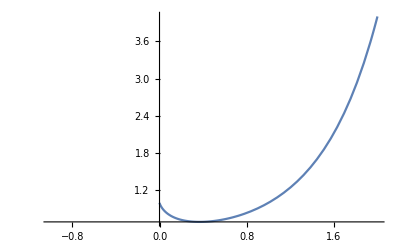

Log plot:

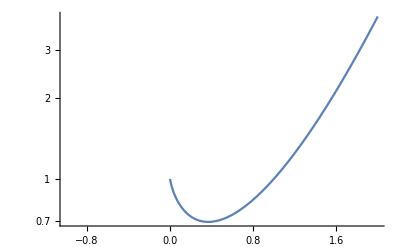

Parametric plot: first specifies x, second specifies y

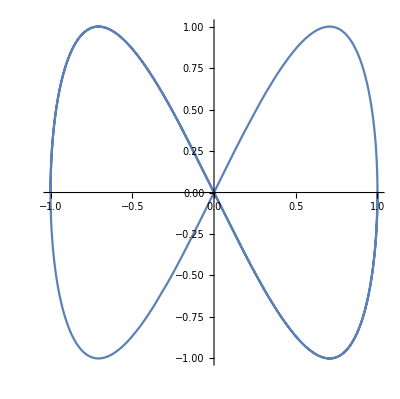

Region plot: plot inequalities

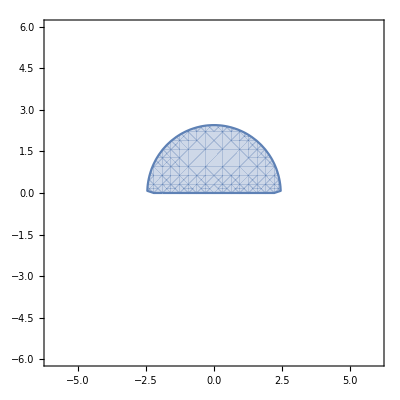

Polar plot

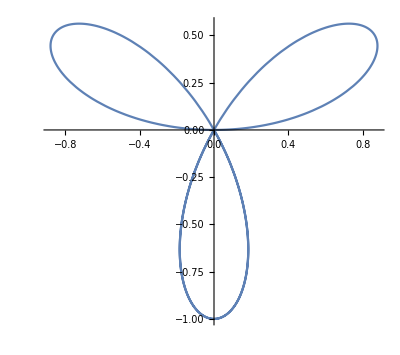

Plotting multiple functions together:

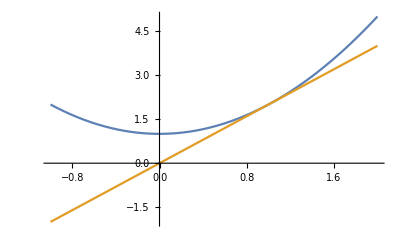

```mathematica
Plot[{1+x^2,2*x},{x,-1,2}]
```

Plotting user defined functions:

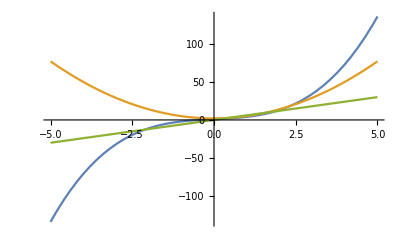

```mathematica
Clear[f]
f[x_]:=x^3+2x+1
Plot[{f[x],f'[x],f''[x]},{x,-5,5}]
Clear[f]
```

Piece wise function:

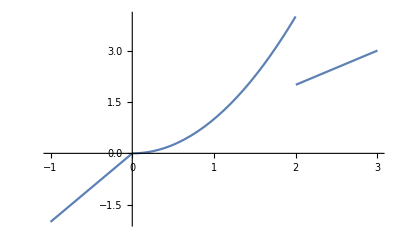

```mathematica
Clear[h]
h[x_]:=Piecewise[{{2x, x<0}, {x^2, 0<=x<=2}, {x, x>2}}]
Plot[h[x],{x,-1,3}]
```

Underlying plotting tech
Triple-click the curve -> computational mesh



```mathematica
Plot[Sin[x],{x,0,2π}]
```

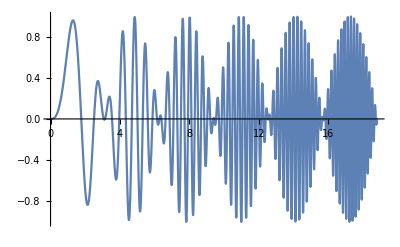

```mathematica
Plot[Sin[x]Sin[x^2],{x,0,6π}]
```

3D Plot

```mathematica
ParametricPlot3D[{4+(3+Cos[v])Sin[u],4+(3+Cos[v])Cos[u],Sin[v]},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[x y],Cos[x y]},{x,-3,3},{y,-3,3},Mesh->None]
```

-Graphics3D-

Revolution plot 3D

```mathematica
RevolutionPlot3D[Sin[t],{t,5π,10π}]
```

-Graphics3D-

Vector Plot

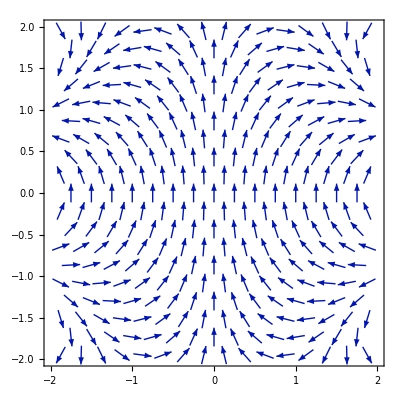

```mathematica
VectorPlot[{Sin[x y],Cos[x y]},{x,-2,2},{y,-2,2}]
```

```mathematica
VectorPlot3D[{Sin[x  z],Cos[ y z],z},{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

Stream Plot

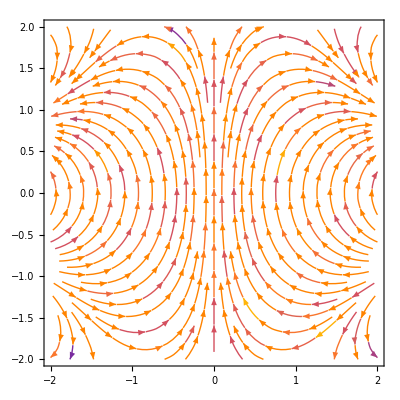

```mathematica
StreamPlot[{Sin[x y],Cos[x y]},{x,-2,2},{y,-2,2}]
```

Graph:

```mathematica
Graph[{1->2,2->3,3->2,1->1}]
```

-Graphics-

Number line Plot

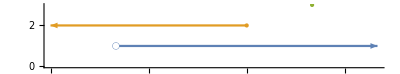

```mathematica
NumberLinePlot[{x>1,x<=3,4},{x,0,5}]
```